## Cornish-Fisher expansion

Determine quantiles of NIG distribution using the Cornish-Fisher expansion

```mathematica
Clear["Global`*"]
```

```mathematica
q[x_]:=√(1+x^2);
g[x_,α_,β_,μ_,δ_]:=(α Exp[δ √(α^2-β^2)-β μ] BesselK[1,δ α q[(x-μ)/δ]] Exp[β x])/(π q[(x-μ)/δ]); (* density function *)
```

```mathematica
M[u_,α_,β_,μ_,δ_]:=Exp[δ (√(α^2-β^2)-√(α^2-(β+u)^2))+μ u] (* moment-generating function *)
```

Cumulant generating function and cumulants

```mathematica
K[t_]:=Log[M[t,α,β,μ,δ]]
κf[r_]:=Module[{t},
D[K[t], {t,r}]/.t->0 (*;
Cumulant[NormalDistribution[],r]*)
]
```

CF from Abramowitz Stegun (uses four cumulants)

```mathematica
γ[r_]:=κf[r+2]/κf[2]^((r+2)/2)
```

```mathematica
h1[x_]:=1/6 HermiteH[2,x];
h2[x_]:=1/24 HermiteH[3,x];
h11[x_]:=-1/36 (2 HermiteH[3,x]+HermiteH[1,x]);
h3[x_]:=1/120 HermiteH[4,x];
h12[x_]:=-1/24 (HermiteH[4,x]+HermiteH[2,x]);
h111[x_]:=1/324 (12 HermiteH[4,x]+19 HermiteH[x,2]);
h4[x_]:=1/720 HermiteH[5,x];
h22[x_]:=-1/384 (3 HermiteH[5,x]+6 HermiteH[3,x]+2 HermiteH[1,x]);
h13[x_]:=-1/180 (2 HermiteH[5,x]+3 HermiteH[3,x]);
h112[x_]:=1/288 (14 HermiteH[5,x]+37 HermiteH[3,x]+8 HermiteH[1,x]);
h1111[x_]:=-1/7776(252 HermiteH[5,x]+832 HermiteH[3,x]+227 HermiteH[1,x]);
```

```mathematica
w[x_]:=x+γ[1] h1[x]\
+γ[2] h2[x]+γ[1]^2 h11[x]\
+γ[3] h3[x]+γ[1] γ[2] h12[x]+γ[1]^3 h111[x]\
+γ[4] h4[x]+γ[2]^2 h22[x]+γ[1] γ[3] h13[x]\
+γ[1]^2 γ[2] h112[x]\
+γ[1]^4 h1111[x];
```

-Graphics-
Version with five cumulants (https://www.value-at-risk.net/the-cornish-fisher-expansion/)

-Graphics-

-Graphics-

```mathematica
Q[θ_,κ_, dist_]:=Module[{q},
q=InverseCDF[dist,θ];

q + (1/6 (q^2-1) κ⟦3⟧) + (1/24 (q^3-3 q) κ⟦4⟧) - 1/36 (2 q^3-5 q) κ⟦3⟧^2 + (1/120 (q^4-6 q^2+3) κ⟦5⟧) - (1/24 (q^4-5 q^2+2) κ⟦3⟧ κ⟦4⟧) + 1/324 (12 q^4-53 q^2+17) κ⟦3⟧^3
]
```

```mathematica
Q[θ_,κ_]:=Q[θ,κ,NormalDistribution[]]
QStudentT[θ_,κ_,ν_]:=Q[θ,κ,StudentTDistribution[ν]]
```

```mathematica
β=0;
α=1;
μ=β^3/α^2-β;
δ=((α^2-β^2)^(3/2))/α^2;
μIG=δ/(√(α^2-β^2));
λ=δ^2;
```

```mathematica
{α,β,μ,δ}
```

{1,0,0,1}

```mathematica
N[κ=Table[κf[r], {r,1,5}]]
```

{0.,1.,0.,0.,0.}

```mathematica
Table[Cumulant[NormalDistribution[],r], {r,1,4}]
```

{0,1,0,0}

```mathematica
n=500000;
Y=RandomVariate[NormalDistribution[],n];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
Z=μ+β W+√W Y;
```

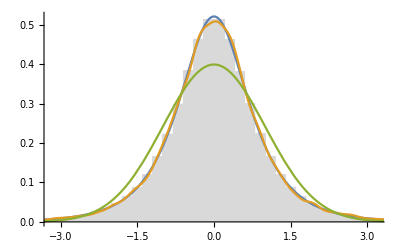

```mathematica
Show[
Histogram[Z, Automatic, "PDF",ChartStyle->LightGray],
Plot[{g[x, α,β,μ,δ],PDF[SmoothKernelDistribution[Z[[1;;20000]]], x],PDF[NormalDistribution[],x]}, {x,-4,4}]
]
```

Empirical VaR

```mathematica
θ=0.99; (* VaR level *)
VaR[X_, θ_]:=-Quantile[X, 1-θ]
VaRNorm[X_,θ_]:=VaR[(X-Mean[X])/StandardDeviation[X], θ]
```

```mathematica
{VaR[Z,θ], VaRNorm[Z,θ]}
```

{2.70046,2.70418}

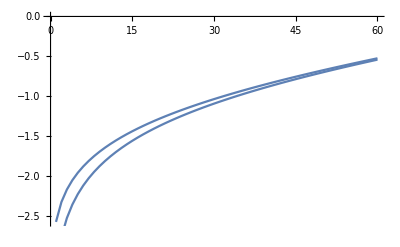

```mathematica
Show[ListPlot[Table[w[InverseCDF[NormalDistribution[],q]] , {q,0.005, 0.3,0.005}],Joined->True],
ListPlot[Table[ w[InverseCDF[StudentTDistribution[10],q]], {q,0.005, 0.3,0.005}],Joined->True]
]
```

```mathematica
{VaR[Z, θ],-QStudentT[1-θ,κ,100],-Q[1-θ,κ],-w[InverseCDF[StudentTDistribution[100],1-θ]],-w[InverseCDF[NormalDistribution[],1-θ]]}
```

{2.70046,2.36422,2.32635,2.36422,2.32635}

```mathematica
NMinimize[{(VaRNorm[Z,θ]+QStudentT[1-θ,κ,ν])^2,ν>3},ν]
```

{0.108065,{ν→315259.}}

```mathematica
TimeConstrained[NMinimize[{(VaRNorm[Z,θ]+w[InverseCDF[StudentTDistribution[ν],1-θ]])^2,ν>3},ν], 60]
```

$Aborted

```mathematica
QStudentT[θ_,κ_]:=QStudentT[θ,κ,60]
```

```mathematica
Timing[t=Table[{VaRNorm[Z,θ], -Q[1-θ,κ]}, {θ,0.005, 0.995, 0.005}];]
Timing[t2=Table[{VaRNorm[Z,θ], -QStudentT[1-θ,κ]}, {θ,0.005, 0.995, 0.005}];]
Timing[t3=Table[{VaRNorm[Z,θ],Abs[VaRNorm[Z,θ]+Q[1-θ,κ]]}, {θ,0.005, 0.995, 0.005}];]
Timing[t4=Table[{VaRNorm[Z,θ],Abs[VaRNorm[Z,θ]+QStudentT[1-θ,κ]]}, {θ,0.005, 0.995, 0.005}];]
Timing[t5 = Table[{VaRNorm[Z,θ], -w[InverseCDF[NormalDistribution[],1-θ]]}, {θ, 0.005, 0.995, 0.005}];]
Timing[t6= Table[{VaRNorm[Z,θ], -w[InverseCDF[StudentTDistribution[82],1-θ]]}, {θ, 0.005, 0.995, 0.005}];]
Timing[t7=Table[{VaRNorm[Z,θ],Abs[VaRNorm[Z,θ]+w[InverseCDF[NormalDistribution[],1-θ]]]}, {θ,0.005, 0.995, 0.005}];]
Timing[t8=Table[{VaRNorm[Z,θ],Abs[VaRNorm[Z,θ]+w[InverseCDF[StudentTDistribution[60],1-θ]]]}, {θ,0.005, 0.995, 0.005}];]
```

{3.39591,Null}

{3.24078,Null}

{6.29206,Null}

{6.52795,Null}

{7.13597,Null}

{7.0005,Null}

{9.86291,Null}

{9.86811,Null}

Relative error

```mathematica
Timing[t9=Table[{VaRNorm[Z,θ],Abs[VaRNorm[Z,θ]+w[InverseCDF[NormalDistribution[],1-θ]]]/Abs[VaRNorm[Z,θ]]},{θ,0.005,0.995,0.005}];]
Timing[t10=Table[{VaRNorm[Z,θ],Abs[VaRNorm[Z,θ]+w[InverseCDF[StudentTDistribution[60],1-θ]]]/Abs[VaRNorm[Z,θ]]},{θ,0.005,0.995,0.005}];]
```

{12.9971,Null}

{12.9774,Null}

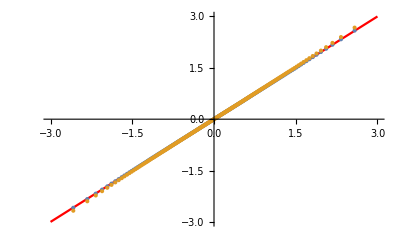

```mathematica
Show[
Plot[x, {x,-3,3},PlotStyle->Red],
ListPlot[{t,t2},PlotRange->All]
]
```

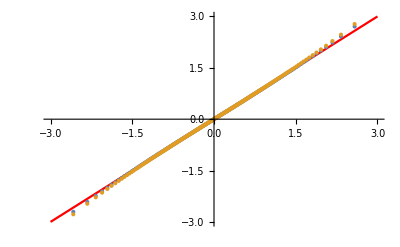

```mathematica
Show[
Plot[x, {x,-3,3},PlotStyle->Red],
ListPlot[{t5,t6},PlotRange->All]
]
```

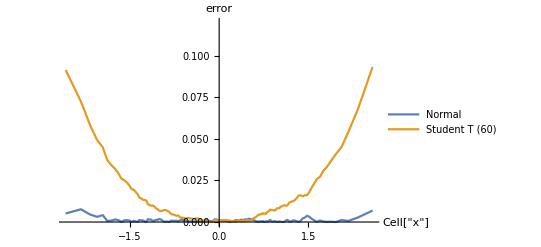

```mathematica
p=ListPlot[{t3,t4},PlotRange->{0,0.12},Joined->True,AxesLabel->{"Cell["x",ExpressionUUID->"eff91e8b-6918-4017-8797-b98c01af7684"]", "error"},PlotLegends->Placed[{"Normal", "Student T (60)"},Above]]
```

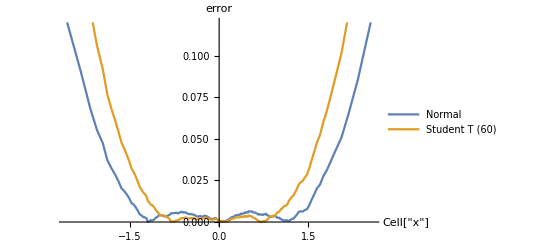

```mathematica
p=ListPlot[{t7,t8},PlotRange->{0, 0.12},Joined->True,AxesLabel->{"Cell["x",ExpressionUUID->"70482db4-779f-4991-a724-40b223f29b60"]", "error"},PlotLegends->Placed[{"Normal", "Student T (60)"},Above]]
```

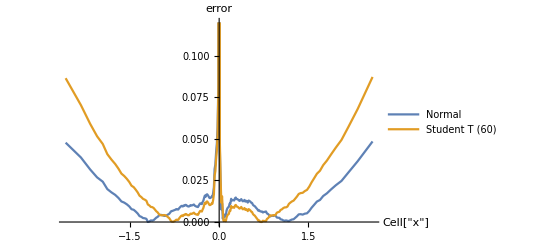

```mathematica
p=ListPlot[{t9,t10},PlotRange->{0,0.12},Joined->True,AxesLabel->{"Cell["x",ExpressionUUID->"8afb6985-d3f6-4442-9c26-92ffeb80d0d6"]", "error"},PlotLegends->Placed[{"Normal", "Student T (60)"},Above]]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/CFerror.pdf", p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/CFerror.pdf

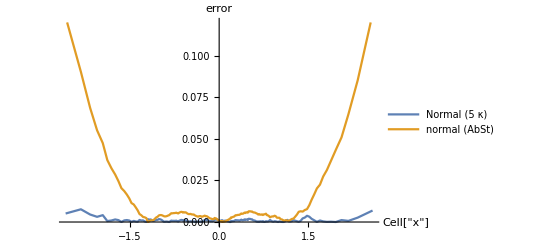

```mathematica
p=ListPlot[{t3,t7},PlotRange->{0,0.12},Joined->True,AxesLabel->{"Cell["x",ExpressionUUID->"acad885e-0f20-4a97-a125-9e299d99b664"]", "error"},PlotLegends->Placed[{"Normal (5 κ)", "normal (AbSt)"},Above]]
```

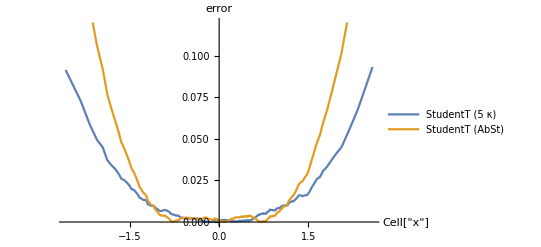

```mathematica
p=ListPlot[{t4,t8},PlotRange->{0,0.12},Joined->True,AxesLabel->{"Cell["x",ExpressionUUID->"24c5300b-b129-4d90-90e6-b855e487bd2d"]", "error"},PlotLegends->Placed[{"StudentT (5 κ)", "StudentT (AbSt)"},Above]]
```

```mathematica
d=EmpiricalDistribution[(Z-Mean[Z])/StandardDeviation[Z]];
```

```mathematica
t=Table[{Q[θ,κ],θ}, {θ, 0.01, 0.99, 0.01}];
t2=Table[{QStudentT[θ,κ],θ}, {θ, 0.01, 0.99, 0.01}];
t3=Table[{Q[θ,κ],θ-CDF[d,Q[θ,κ]]}, {θ, 0.005, 0.995, 0.005}];
t4=Table[{QStudentT[θ,κ],θ-CDF[d,QStudentT[θ,κ]]}, {θ, 0.005, 0.995, 0.005}];
t5=Table[{VaRNorm[Z,1-θ],(1-θ)-CDF[d,VaRNorm[Z,1-θ]]}, {θ, 0.005, 0.995, 0.005}];
```

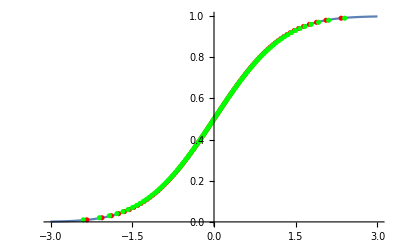

```mathematica
Show[
Plot[CDF[d,x], {x,-3,3}],
ListPlot[{t,t2}, PlotStyle->{Red,Green}]
]
```

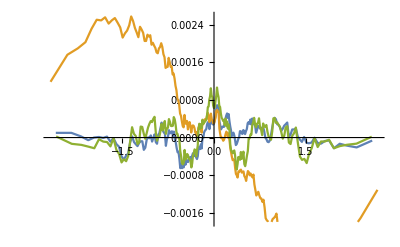

```mathematica
ListPlot[{t3,t4,t5},Joined->True]
```